alpha^2+3 alpha eta k-350. k^2 (1-0.01 k^2)==0

70

1

0.1

0

1

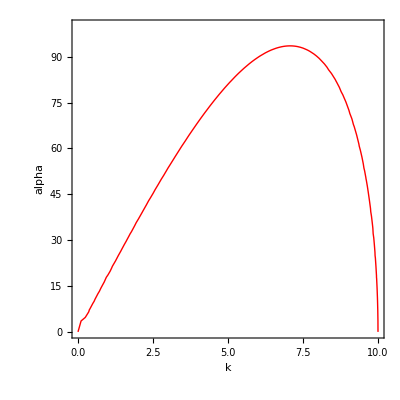

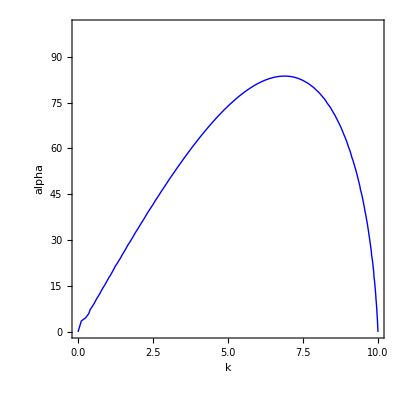

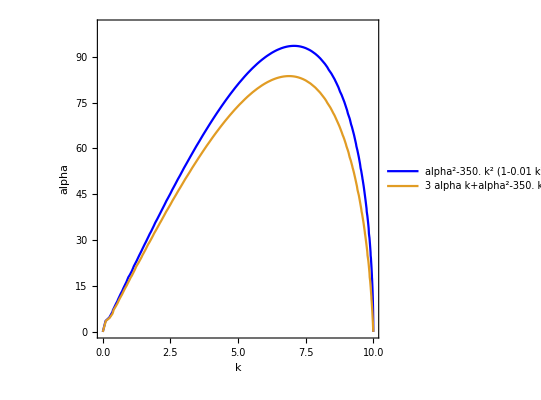

{93.5414,{alpha→93.5414,k→7.07107}}

{83.6568,{alpha→83.6568,k→6.88448}}

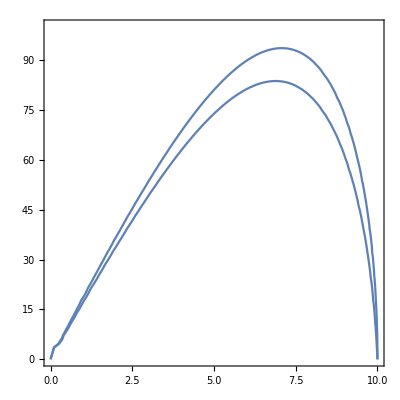

```mathematica
alpha^2+3*k/rho*eta*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0
sigma=70
rho=1
a=0.1
eta0=0
eta1=1
g1=ContourPlot[{alpha^2+3*k/rho*eta0*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0},{k,0,10},{alpha,0,100},ContourStyle->{{Red,Thick}},FrameLabel->{"k","alpha"},PlotLegends->"Expressions"]
g2=ContourPlot[{alpha^2+3*k/rho*eta1*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0},{k,0,10},{alpha,0,100},ContourStyle->{{Blue,Thick}},FrameLabel->{"k","alpha"},PlotLegends->"Expressions"]

ContourPlot[{alpha^2+3*k/rho*eta0*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0,alpha^2+3*k/rho*eta1*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0},{k,0,10},{alpha,0,100},ContourStyle->{Blue,Thick{Red,Thick}},FrameLabel->{"k","alpha"},PlotLegends->"Expressions"]
Maximize[alpha,{alpha^2+3*k/rho*eta0*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0},{alpha,k}]
Maximize[alpha,{alpha^2+3*k/rho*eta1*alpha-sigma*k^2/(2*rho*a)*(1-k^2*a^2)==0},{alpha,k}]
```